```mathematica
Exit
```

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]]
```

```mathematica
ClearAll[pFourier,pHorner,cpHorner];

pFourier[n_]:=pFourier[n]=Block[{x},Function@@{x,FourierTransform[Sinc[s]^n,s,x]}];

pHorner[n_]:=pHorner[n]=Block[{qexp,x},
qexp=PiecewiseExpand[
pFourier[n][x]/.Sign[x_]:>Piecewise[{{-1,x<0},{1,x>0}}]
];
qexp[[1,All,1]]=HornerForm/@qexp[[1,All,1]];
Function@@{x,qexp}
];

cpHorner[n_]:=cpHorner[n]=Block[{x},
With[{code=pHorner[n][x]},
Compile[{{x,_Real}},code,
CompilationTarget->"C",
RuntimeAttributes->{Listable},
Parallelization->True,
RuntimeOptions->"Quality"
]
]
];

ClearAll[pBSpline];
pBSpline[n_]:=pBSpline[n]=Block[{x},Function@@{x,Sqrt[π/2] BSplineBasis[n-1,0,((x+n)/(2n))]}];

ClearAll[DpBSpline];
DpBSpline[n_]:=DpBSpline[n]=Block[{x},Function@@{x,D[pBSpline[n][x],x]}]
```

```mathematica
??RectangleConvolutionPower
```

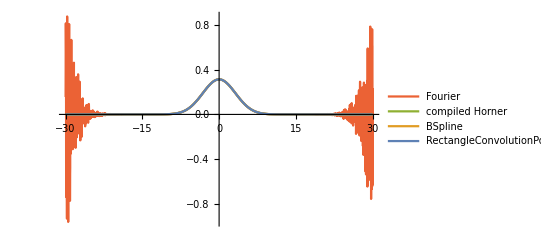

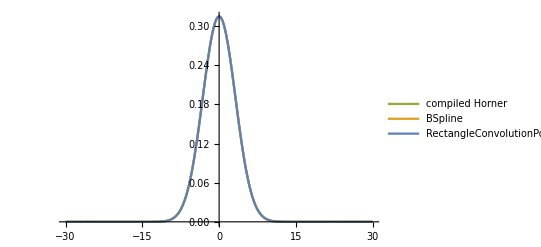

```mathematica
n=30;
(*This plot shows that the expression obtained from direct Fourier transform is very unstable.*)
Plot[{pFourier[n][x],cpHorner[n][x],pBSpline[n][x],RectangleConvolutionPower[x,n]},{x,-n,n},
PlotRange->All,PlotLegends->{"Fourier","compiled Horner","BSpline","RectangleConvolutionPower"},
PlotStyle->ColorData[97]/@Range[4,1,-1]
]

(*From afar, the other implementations look equally good...*)
Plot[{cpHorner[n][x],pBSpline[n][x],RectangleConvolutionPower[x,n]},{x,-n,n},
PlotRange->All,
PlotLegends->{"compiled Horner","BSpline","RectangleConvolutionPower"},
PlotStyle->ColorData[97]/@Range[3,1,-1]
]
```

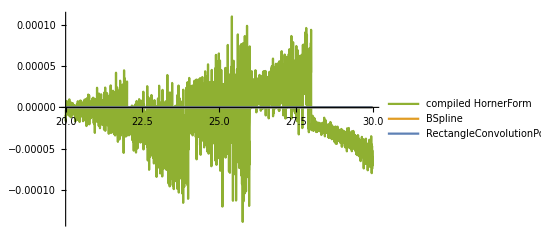

```mathematica
(*... but a close-up shows that the Horner form has some severe problems in the tails.*)
Plot[{cpHorner[n][x],pBSpline[n][x],RectangleConvolutionPower[x,n]},{x,20,n},
PlotRange->All,
PlotLegends->{"compiled HornerForm","BSpline","RectangleConvolutionPower"},
PlotStyle->ColorData[97]/@Range[3,1,-1]
]
```

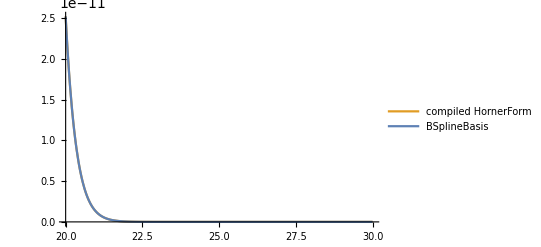

```mathematica
(*The Cox-de Boor implementation do not seem to have these problems.*)
Plot[{pBSpline[n][x],RectangleConvolutionPower[x,n]},{x,20,n},
PlotRange->All,
PlotLegends->{"compiled HornerForm","BSplineBasis","RectangleConvolutionPower"},
PlotStyle->ColorData[97]/@Range[2,1,-1]
]
```

General::munfl: 1.02143×10^-6 7.62375×10^-303 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.049999 1.55742×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.02143×10^-6 1.55742×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

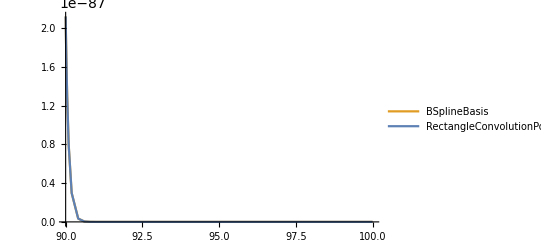

```mathematica
(*Even for n=100, the Cox-de Boor implementations do not seem to have these stability issues.*)
(*BSplineBasis just complaines about numbers too tiny to represent in double precision.*)
n=100;
Plot[{pBSpline[n][x],RectangleConvolutionPower[x,n]},{x,90,n},
PlotRange->All,
PlotLegends->{"BSplineBasis","RectangleConvolutionPower"},
PlotStyle->ColorData[97]/@Range[2,1,-1]
]
```

```mathematica
(*Let's make a performance comparison.*)
n=30;
count=100000;
xlist=Subdivide[-N[n],N[n],count-1];

aa=cpHorner[n][xlist];//RepeatedTiming//First
bb=pBSpline[n]/@xlist;//Quiet//RepeatedTiming//First
cc=RectangleConvolutionPower[xlist,n];//RepeatedTiming//First

(* On my machine calling RectangleConvolutionPower on a list of arguments is about 1200 times faster then Mathematica's BSplineBasis.*)
```

0.0229193

7.86566

0.00659746

```mathematica
(*Plotting thins, we see the problem of the HornerForm in the tails, once again.*)
ListLinePlot[{aa,bb,cc},
DataRange->{-n,n},
PlotRange->All,
PlotLegends->{"compiled Horner","BSpline","RectangleConvolutionPower"},
PlotStyle->ColorData[97]/@Range[3,1,-1]
]
```

-Graphics-

0.0270083

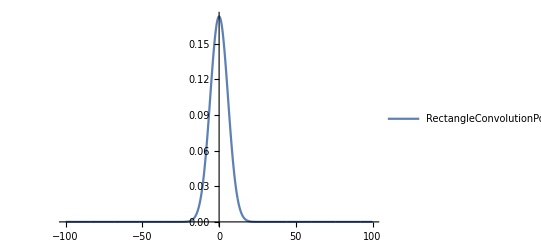

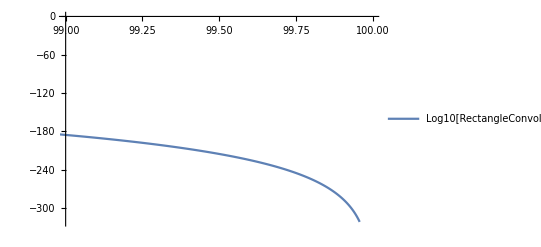

```mathematica
(*Even for n = 300 it seems to work fine. It only takes a bit longer because Cox-de Boor's runtime is quadratic in n =( .*)

(*But maybe we can resolve this by creating a low-order spline interpolant.*)
n=100;
count=100000;
xlist=Subdivide[-N[n],N[n],count-1];
vals=RectangleConvolutionPower[xlist,n];//RepeatedTiming//First

ListLinePlot[{vals},
DataRange->{-n,n},
PlotRange->All,
PlotLegends->{"RectangleConvolutionPower"},
PlotStyle->ColorData[97]/@Range[1,1,-1]
]

ListLinePlot[{Log10[vals]},
DataRange->{-n,n},
PlotRange->{{n-1,n},All},
PlotLegends->{"Log10[RectangleConvolutionPower]"},
PlotStyle->ColorData[97]/@Range[1,1,-1]
]
```

```mathematica
times=Table[
{n,RepeatedTiming[RectangleConvolutionPower[Subdivide[-N[n],N[n],100000-1],n]][[1]]},
{n,10,300,10}];
```

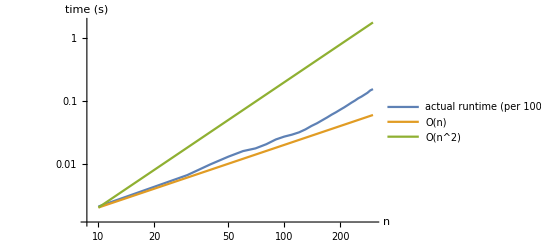

```mathematica
O1=Table[{n,2/10000.n},{n,10,300,10}];
O2=Table[{n,2/100000.n^2},{n,10,300,10}];
ListLinePlot[{times,O1,O2},
ScalingFunctions->{"Log","Log"},
PlotLegends->{"actual runtime (per 10000)","O(n)","O(n^2)"},
AxesLabel->{"n","time (s)"}
]
```

```mathematica
r/(2n)
```

```mathematica
sampleCount=100000;
n=30;
xdata=RandomPoint[Sphere[],{100000,n}];
rdata=Sqrt[Total[Total[X,{2}]^2,{2}]];
```

```mathematica
r=.
```

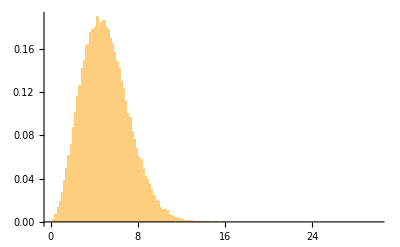

```mathematica
background=Histogram[rdata,"Wand","PDF",PlotRange->{{0,n},All}]
```

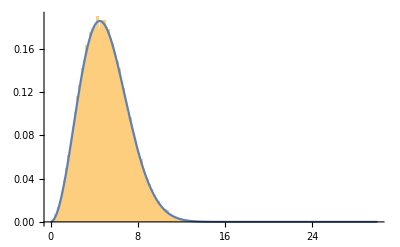

```mathematica
Show[
background,
Plot[RandomFlightPDF[r,n],{r,0,n}]
]
```

```mathematica
RandomFlightPDF[r_,n_Integer?Positive]:=(-Sqrt[2/Pi]r) RectangleConvolutionPower'[r,n];
```

r/60

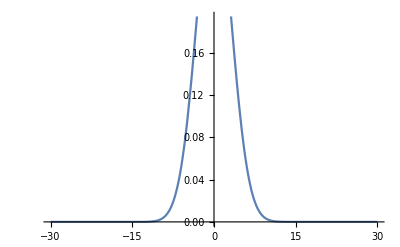

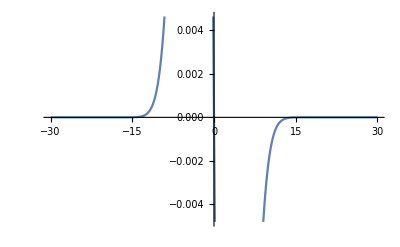

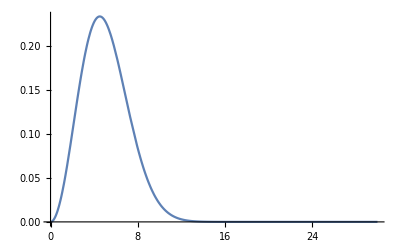

```mathematica
Plot[RectangleConvolutionPower[r,n],{r,-n,n}]
Plot[RectangleConvolutionPower'[r,n],{r,-n,n}]
```